## Set up the models and the standard parameters

The goal here is to re-connect the ideas of the models and the parameters we had before to try and think about some implied landscape where we can see what the distribution is of the probability that some organisms will end up using the same space on a landscape.

```mathematica
baseDir="/Users/colebrookson/github/theRmal-landscape/";
figsDir=FileNameJoin[{baseDir,"figs"}];
relativePath[parts__]:=FileNameJoin[{baseDir,parts}];
```

```mathematica
(*Define constants*)
R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;
δ=0.5;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Define grid size for the landscape*)
gridSize={50,50}; (*adjust for larger or smaller landscapes*)

(*Generate random values for T and S across the grid*)
meanT = 20;
varT = 5;
alphaS = 1.2;
betaS = 1;
Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];

(*Compute probabilities w_{i,j} across the landscape*)
(*Truncate landscape probabilities to be>=0*)
landscapeProbabilities=Table[Max[0,w[Tgrid[[i,j]],Sgrid[[i,j]]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];
```

```mathematica
(*Heatmap for w_{i,j} values with Magma color scheme*)heatmapW=ArrayPlot[landscapeProbabilities,ColorFunction->"Pastel",Mesh->False,PlotLabel->"Probability Landscape (w_{i,j} ≥ 0)",PlotLegends->Automatic];

(*Heatmap for T values with TemperatureMap color scheme*)
heatmapT=ArrayPlot[Tgrid,ColorFunction->"TemperatureMap",Mesh->False,PlotLabel->"Temperature (T) Landscape",PlotLegends->Automatic];

(*Heatmap for S values with purple gradient color scheme*)
heatmapS=ArrayPlot[Sgrid,ColorFunction->(Blend[{White,Purple},#]&),Mesh->False,PlotLabel->"Supply (S) Landscape",PlotLegends->Automatic];


(*Arrange the plots in a grid with T and S on the top row,w at double size on the second row*)
threeArray = GraphicsGrid[{{Style[heatmapT, FontSize->Scaled[0.04]],Style[heatmapS, FontSize->4],Style[heatmapW, FontSize->4]}},Spacings->{2,1}];
Show[threeArray, ImageSize->6/2.54*300]
Export[relativePath["figs","temp-supply-probability-landscape.pdf"],threeArray, ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

-Graphics-

```mathematica
Head[landscapeProbabilities]
```

## Do two options - one with really heterogeneous patches and one with highly homogenous landscapes (TO-DO)

```mathematica
10/2.54*300
```

1181.1

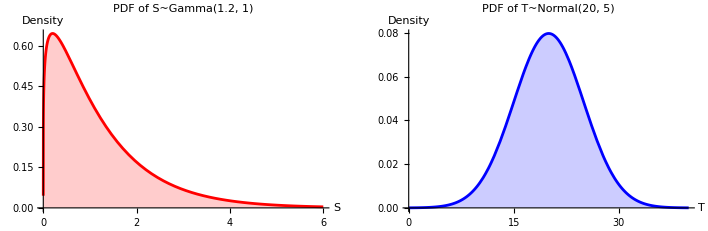

```mathematica
(*Flatten the landscape probabilities for density plot*)
flatProbabilities=Flatten[landscapeProbabilities];

(*Plot as a density plot*)
pdfPlotS=Plot[PDF[GammaDistribution[alphaS,betaS],x],{x,0,6},PlotLabel->Style[Text@StringJoin["PDF of S~Gamma(",ToString[alphaS],", ",ToString[betaS],")"],14],Filling->Axis,PlotStyle->Red,AxesLabel->{"S","Density"},ImageSize->Medium];
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},PlotLabel->Style[Text@StringJoin["PDF of T~Normal(",ToString[meanT],", ",ToString[varT],")"],14],Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium];
hist=Histogram[flatProbabilities,{0, 1, 0.01},"Probability",PlotLabel->Style[Text@StringJoin["Histogram of w_ij"],14]];

(*Display all three plots*)
SandTPDFS = GraphicsGrid[{{Style[pdfPlotS, FontSize->Scaled[0.04]],Style[pdfPlotT, FontSize->4]}}];
Show[SandTPDFS, ImageSize->6/2.54*300]
Export[relativePath["figs","temp-supply-wij-pdfs.pdf"],SandTPDFS, ImageSize -> 6/2.54*300, ImageResolution -> 1200];
(*GraphicsGrid[{{pdfPlotS,pdfPlotT},{hist}},Spacings->{1,2}]*)
```

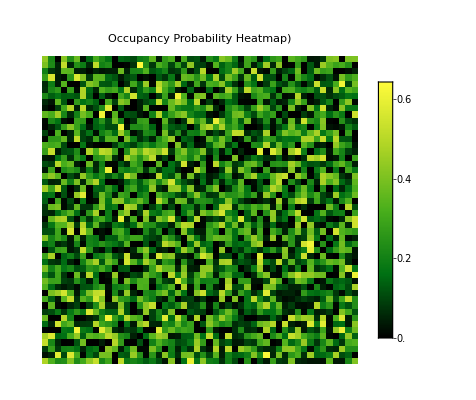

```mathematica
(*Calculate the probability that two organisms occupy the same place*)
occupancyProbability=landscapeProbabilities^2;
heatmapO=ArrayPlot[occupancyProbability,ColorFunction->"AvocadoColors",Mesh->False,PlotLabel->"Occupancy Probability Heatmap)",PlotLegends->Automatic];
heatmapO
```

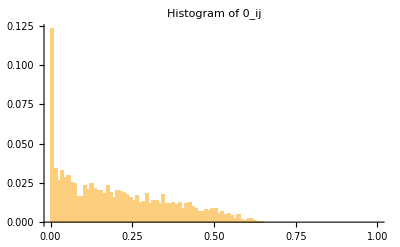

```mathematica
histO=Histogram[Flatten[occupancyProbability],{0, 1, 0.01},"Probability",PlotLabel->Style[Text@StringJoin["Histogram of 0_ij"],14]];
histO
```

```mathematica
(*Step 1:Normalize landscapeProbabilities*)
totalSum=Total[Total[landscapeProbabilities]];
numIndividuals= 2;
normalizedProbabilities=landscapeProbabilities/totalSum;

(*Step 2:Calculate the probability that two organisms choose the same cell*)
occupancyProb=Total[Total[normalizedProbabilities^2]];
occupancyProb

(*Display the co-occupancy probability*)
occupancyProb//numIndividuals
```

```mathematica
0.0005192332802559322
```

## Co-occurrence probabilities as a function of temperature

So now, we want to state that each normalized probability is:

  
And then $C$ will always be the sum across these normalized probabilities.

```mathematica
(*Step 1:Calculate normalized probabilities x_{i,j}*)totalSum=Total[Total[landscapeProbabilities]];
normalizedProbabilities=landscapeProbabilities/totalSum;

(*Step 2:Calculate normalized co-occurrence probabilities (x_{i,j}^2)*)
normalizedCoOccurrence=normalizedProbabilities^2;

(*Step 3:Plot normalized co-occurrence probabilities with a blue-to-red gradient*)
coOccurrenceHeatmap=ArrayPlot[normalizedCoOccurrence,ColorFunction->(Blend[{Blue,Red},#]&),Mesh->True,PlotLabel->"Normalized Co-Occurrence Probability Landscape (x_{i,j}^2)",PlotLegends->Automatic];

(*Display the heatmap*)
coOccurrenceHeatmap = GraphicsGrid[{{Style[coOccurrenceHeatmap, FontSize->Scaled[0.04]]}}];
coOccurrenceHeatmap
Export[relativePath["figs","cooccurence-heatmaps.pdf"],coOccurrenceHeatmap, ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

-Graphics-

```mathematica
(*Given Parameters*)
(*Given Parameters*)R0=0.5;
gamma=150;
ma=0.01;mb=0.1;mc=0.05;
TI=20;

(*Define Imax and m functions*)
Imax[T_]:=Exp[-((T-TI)^2)/gamma];
m[T_]:=ma Exp[mb T]+mc;

(*Check the dimensions of the Tgrid and Sgrid*)
dimensionsTgrid=Dimensions[Tgrid];
dimensionsSgrid=Dimensions[Sgrid];

(*Print the dimensions to ensure they match*)
Print["Dimensions of Tgrid: ",dimensionsTgrid];
Print["Dimensions of Sgrid: ",dimensionsSgrid];

(*Test calculation for a single point in the grid*)
testConsumerCount=(Imax[Tgrid[[1,1]]]*Sgrid[[1,1]])/(Sgrid[[1,1]]+R0)-m[Tgrid[[1,1]]];

Print["Test consumer count at (1,1): ",testConsumerCount];

(*If all looks good,calculate the entire grid using Table*)
consumerCountGrid=Table[(Imax[Tgrid[[i,j]]]*Sgrid[[i,j]])/(Sgrid[[i,j]]+R0)-m[Tgrid[[i,j]]],{i,Length[Tgrid]},{j,Length[Tgrid[[1]]]}];

(*Calculate total number of consumers by summing all the values in the grid*)
totalConsumers=Total[consumerCountGrid,2]//Total;

(*Display the total number of consumers*)
Print["Total number of consumers across the landscape: ",totalConsumers];

(*Plot consumer count as a heatmap*)
consumerCountHeatmap=ArrayPlot[consumerCountGrid,ColorFunction->(Blend[{Blue,Green,Yellow,Red},#]&),Mesh->True,PlotLabel->"Consumer Count Landscape",PlotLegends->Automatic,ImageSize->Large];

(*Display the heatmap*)
consumerCountHeatmap
```

Dimensions of Tgrid: {50,50}

Dimensions of Sgrid: {50,50}

Test consumer count at (1,1): 0.660815

Total number of consumers across the landscape: 957.461

-Graphics-

```mathematica
|
```

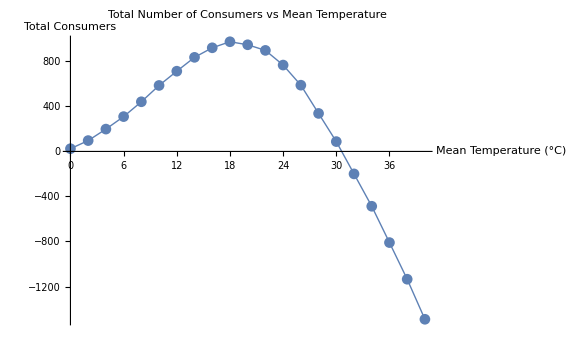

```mathematica
(*Given Constants*)R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
gamma=150;
delta=0.5;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/gamma];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Define grid size for the landscape*)
gridSize={50,50}; (*Adjust for larger or smaller landscapes*)

(*Generate random values for S across the grid (temperature will vary)*)
alphaS=1.2;
betaS=1;
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];

(*Function to calculate total consumers for a given meanT*)
calculateConsumers[meanT_]:=Module[{Tgrid,consumerCountGrid,totalConsumers},(*Generate random values for T based on meanT*)varT=5;(*Define the variance for T*)Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
(*Calculate the consumer count across the entire grid*)consumerCountGrid=Table[(Imax[Tgrid[[i,j]]]*Sgrid[[i,j]])/(Sgrid[[i,j]]+R0)-m[Tgrid[[i,j]]],{i,Length[Tgrid]},{j,Length[Tgrid[[1]]]}];
(*Calculate total consumers by summing all the values in the grid*)totalConsumers=Total[consumerCountGrid,2]//Total;
totalConsumers];

(*Range of meanT values to explore*)
meanTValues=Range[0,40,2];  (*From 0 to 40 in steps of 2*)

(*Use ParallelTable to calculate the total number of consumers for each meanT*)
consumerCounts=ParallelTable[calculateConsumers[meanT],{meanT,meanTValues}];

(*Plot the results as a line plot*)
consumerCountPlot=ListLinePlot[Transpose[{meanTValues,consumerCounts}],PlotLabel->"Total Number of Consumers vs Mean Temperature",AxesLabel->{"Mean Temperature (°C)","Total Consumers"},PlotStyle->Thick,ImageSize->Large,PlotMarkers->Automatic];

(*Display the plot*)
consumerCountPlot
```

## Calculate the likelihood that two individuals independently choose the same cell anywhere on the landscape

```mathematica
(*Constants*)
R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
gamma=150;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/gamma];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Generate random temperature (T) and supply (S) grids*)
gridSize={50,50}; (*Adjust grid size as needed*)

(*Example random generation of T and S grids*)
meanT=20;varT=5;
alphaS=1.2;betaS=1;
Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];

(*Calculate the selection probabilities w for each grid cell*)
wGrid=Table[w[Tgrid[[i,j]],Sgrid[[i,j]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];

(*Normalize the wGrid to ensure it sums to 1*)
normalizedWGrid=wGrid/Total[Flatten[wGrid]];

(*Calculate C as the sum of squared normalized probabilities*)
c=Total[Flatten[Table[normalizedWGrid[[i,j]]^2,{i,gridSize[[1]]},{j,gridSize[[2]]}]]]
```

0.000534832

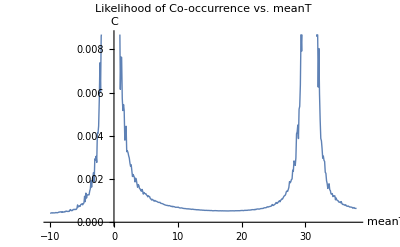

```mathematica
(*Constants*)R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
gamma=150;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-20)^2)/gamma];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Generate random supply (S) grid*)
gridSize={50,50}; (*Adjust grid size as needed*)

alphaS=1.2;betaS=1;
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];

(*Function to calculate C for a given meanT*)
calcC[meanT_]:=Module[{Tgrid,wGrid,normalizedWGrid,C},
(*Generate random temperature (T) grid for current meanT*)Tgrid=RandomVariate[NormalDistribution[meanT,5],gridSize];
(*Calculate the selection probabilities w for each grid cell*)wGrid=Table[w[Tgrid[[i,j]],Sgrid[[i,j]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];
(*Normalize the wGrid to ensure it sums to 1*)normalizedWGrid=wGrid/Total[Flatten[wGrid]];
(*Calculate C as the sum of squared normalized probabilities*)C=Total[Flatten[Table[normalizedWGrid[[i,j]]^2,{i,gridSize[[1]]},{j,gridSize[[2]]}]]];
Return[C]];

(*Parallelize the calculations over meanT from 0 to 40 in increments of 0.1*)
meanTValues=Range[-10,38,0.1];
CValues=ParallelMap[calcC,meanTValues];

(*Plot the results*)
ListLinePlot[Transpose[{meanTValues,CValues}],PlotLabel->"Likelihood of Co-occurrence vs. meanT",AxesLabel->{"meanT","C"},PlotStyle->Thick]
```

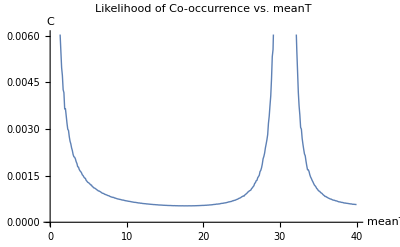

β_(i j)

0.39

```mathematica
(*Function to calculate C for a given meanT with 100 samples*)calcC[meanT_]:=Module[{Tgrid,wGrid,normalizedWGrid,CValues,C},(*Generate 100 random temperature grids for current meanT*)CValues=Table[Tgrid=RandomVariate[NormalDistribution[meanT,5],gridSize];
(*Calculate the selection probabilities w for each grid cell*)wGrid=Table[w[Tgrid[[i,j]],Sgrid[[i,j]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];
(*Normalize the wGrid to ensure it sums to 1*)normalizedWGrid=wGrid/Total[Flatten[wGrid]];
(*Calculate C as the sum of squared normalized probabilities*)C=Total[Flatten[Table[normalizedWGrid[[i,j]]^2,{i,gridSize[[1]]},{j,gridSize[[2]]}]]];
C,{10}  (*100 samples for each meanT*)];
(*Return the average of the 100 C values*)Return[Mean[CValues]];];

(*Parallelize the calculations over meanT from 0 to 40 in increments of 0.1*)
meanTValues=Range[0,40,0.1];
CValues=ParallelMap[calcC,meanTValues];

(*Plot the results*)
ListLinePlot[Transpose[{meanTValues,CValues}],PlotLabel->"Likelihood of Co-occurrence vs. meanT",AxesLabel->{"meanT","C"},PlotStyle->Thick]
```

## Trying to figure out how to simulate this -- first check that all of my w_ij values sum to 1

```mathematica
(*Define constants*)R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w[T,S]*)
w[T_,S_]:=Max[0,(Imax[T]*S)/(S+R0)-m[T]];

(*Function to compute normalized w[T,S] across a grid*)
normalizedW[gridSize_,meanT_,varT_,alphaS_,betaS_]:=Module[{Tgrid,Sgrid,Wgrid,totalW},(*Generate random grids for T and S*)Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];
(*Compute w[T,S] for each cell*)Wgrid=MapThread[w,{Tgrid,Sgrid},2];
(*Normalize Wgrid to sum to 1*)totalW=Total[Flatten[Wgrid]];
Wgrid/totalW];

(*Example usage*)
gridSize={50,50}; (*Define the grid size*)
meanT=20;          (*Mean temperature*)
varT=5;            (*Variance in temperature*)
alphaS=1.2;        (*Shape parameter for S*)
betaS=1;           (*Scale parameter for S*)

(*Get normalized w[T,S] grid*)
normalizedGrid=normalizedW[gridSize,meanT,varT,alphaS,betaS];

(*Check normalization*)
Total[Flatten[normalizedGrid]] (*Should return 1*)
```

1.

## Now simulate the whole thing:

```mathematica
(*Define constants*)R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;
δ=0.5;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w[T,S]*)
w[T_, S_] := Max[0,(Imax[T]*S)/(S+R0)-m[T]];

(*Function to compute normalized w[T,S] across a grid*)
normalizedW[gridSize_,meanT_,varT_,alphaS_,betaS_]:=Module[{Tgrid,Sgrid,Wgrid,totalW},(*Generate random grids for T and S*)Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];
(*Compute w[T,S] for each cell*)Wgrid=MapThread[w,{Tgrid,Sgrid},2];
(*Normalize Wgrid to sum to 1*)totalW=Total[Flatten[Wgrid]];
Wgrid/totalW];
Wgrid=normalizedW[gridSize,meanT,varT,alphaS,betaS];
```

```mathematica
(*Define the epsilon function*)
epsilon[T_,S_]:=0.2;

(*Compute the probability of disease spreading in a cell,φ_ij(k,I=1)*)
PhiIJ[S_, w_]:=1-(1-w*0.2)^S;

(*Compute the grid of φ_ij values for the entire landscape*)
(*Compute the ϕ(i,j) values for the entire grid*)
PhiGrid=Table[PhiIJ[2,Wgrid[[i,j]]],(*Assume k=1 for this example*){i,gridSize[[1]]},{j,gridSize[[2]]}];
```

```mathematica
(*Plot the φ_ij values on the landscape as a heatmap*)
landscapeProb=ArrayPlot[PhiGrid,ColorFunction->"TemperatureMap",PlotLabel->Style["Disease Spread Probability on Landscape",FontSize->12],FrameLabel->{Style["Grid Y",FontSize->10],Style["Grid X",FontSize->10]},PlotLegends->Placed[Automatic,Below],BaseStyle->{FontSize->6} (*Sets a base font size for all elements*)];
(*landscapeProb = ArrayPlot[PhiGrid,ColorFunction->"TemperatureMap",PlotLabel->"Disease Spread Probability on Landscape",FrameLabel->{"Grid Y","Grid X"}, PlotLegends->Automatic]*)
Export[relativePath["figs","full-landscape-prob.pdf"],landscapeProb, ImageSize -> 2/2.54*300, ImageResolution -> 1200];
(*Calculate the bold ϕ(k,I=1)*)
BoldPhi=Total[Flatten[PhiGrid]]

(*Print the result*)
BoldPhi
```

0.399979

0.399979